# ME-314: Angry Birds Final Project by Siyuan Yu

```mathematica
Quit[];
```

450.

112.5

2.5

1.75

1

1

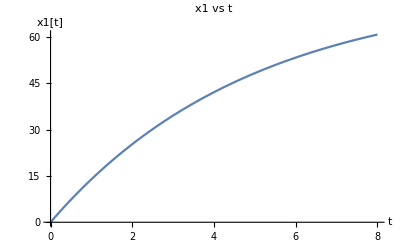

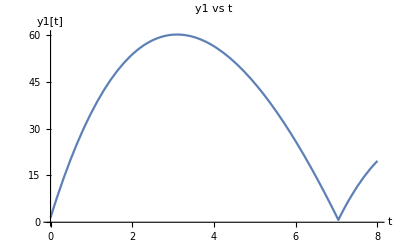

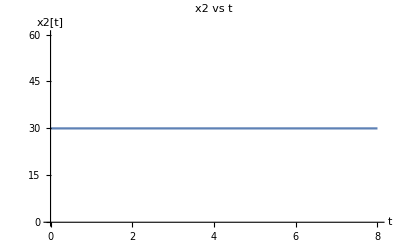

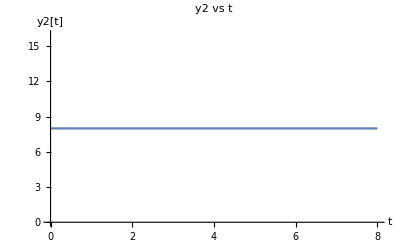

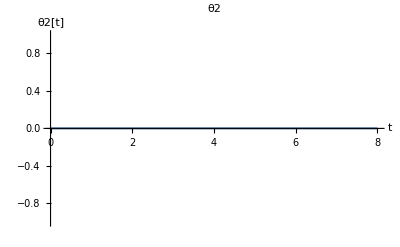

THE PIG IS SAFE... TRY AGAIN!

URLFetch::invhttp: "Failure when receiving data from the peer".

FetchURL::conopen: The connection to URL "http://vignette4.wikia.nocookie.net/angrybirds/images/3/39/Hp.png/revision/20130713090008" cannot be opened. If the URL is correct, you might need to configure your firewall program, or you might need to set a proxy in the Internet connectivity tab of the Preferences dialog (or by calling SetInternetProxy).  For HTTPS connections, you might need to inspect the authenticity of the server's SSL certificate and choose to accept it.

```mathematica
(*Choose Initial Bird Parameters*)

InitialAngle=70;

InitialSpeed=45;

(*Functions*)

unhat2[matrix_]:=matrix[[1,2]];

unhat3[matrix_]:={Flatten[{matrix[[3,2]]}],Flatten[{matrix[[1,3]]}],Flatten[{matrix[[2,1]]}]};

hat2[value_]:={Flatten[{0,-value}],Flatten[{value, 0}]};

hat3[vector_]:={Flatten[{0,-vector[[3]],vector[[2]]}],Flatten[{vector[[3]], 0, -vector[[1]]}],Flatten[{-vector[[2]],vector[[1]],0}]};

homogenize2[rot_,trans_]:={Flatten[{rot[[1,1]],rot[[1,2]],trans[[1,1]]}],Flatten[{rot[[2,1]],rot[[2,2]],trans[[2,1]]}],Flatten[{0,0,1}]};

homogenize3[rot_,trans_]:={Flatten[{rot[[1,1]],rot[[1,2]],rot[[1,3]],trans[[1,1]]}],Flatten[{rot[[2,1]],rot[[2,2]],rot[[2,3]],trans[[2,1]]}],Flatten[{rot[[3,1]],rot[[3,2]],rot[[3,3]],trans[[3,1]]}],Flatten[{0,0,0,1}]};

rotation[θ_]:={Flatten[{Cos[θ],-Sin[θ]}],Flatten[{Sin[θ],Cos[θ]}]};

getω[g_]:=unhat2[(Inverse[g].D[g,t])[[{1,2},{1,2}]]];

getpdot[g_]:={D[g[[{1,2},3]],t]}ᵀ;

getp[g_]:={g[[{1,2},3]]}ᵀ;

(*Initial Parameters, all in SI units*)
	(*Box*)
Boxlength=3;
Boxwidth=1;
Boxρ=300;
Boxt=0.5;
BoxVol=Boxlength*Boxwidth*Boxt;
m2=BoxVol*Boxρ
Ιbox=(m2/12)*(Boxlength*Boxwidth)
	(*Bird*)
RadiusBird=0.75;
m1=2.5;
	(*General*)
gravity=9.8;
q={{x1[t]},{y1[t]},{x2[t]},{y2[t]},{θ2[t]}};
dq=D[q,t];
ddq=D[dq,t];
	(*Pig*)
pigx=37;
RadiusPig=1;

(*Initial Box Constraint*)
yforce=m2*gravity;
box={0,0,0,yforce,0};
Initialx=30;
Initialy=8;

(*Ledge*)
ledget=0.1+Boxwidth;
ledgex=Initialx;
ledgey=Initialy-Boxlength/2-0.01;

	(*Air Drag*)
c=0.47; (*Coefficient of drag*)
ρ=1.225;
A=Pi*RadiusBird^2; (*Area of bird*)
Dragx1=-0.5*ρ*c*A*D[x1[t],t];
Dragy1=-0.5*ρ*c*A*D[y1[t],t];
drag={Dragx1,Dragy1,0,0,0};

(*Transformation Functions*)
rotwa=IdentityMatrix[2];
transwa={{x1[t]},{y1[t]}};

rotwb=rotation[θ2[t]];
transwb={{x2[t]},{y2[t]}};

Subscript[g, wa]=homogenize2[rotwa,transwa];
Subscript[g, wb]=homogenize2[rotwb,transwb];

(*Energies*)
	(*Box*)
Subscript[KE, 2]=(1/2)*m2*getpdot[Subscript[g, wb]]ᵀ.getpdot[Subscript[g, wb]]+(1/2)*getω[Subscript[g, wb]]*Ιbox*getω[Subscript[g, wb]];
Subscript[PE, 2]=m2*gravity*getp[Subscript[g, wb]]ᵀ.{{0},{1}};

	(*Bird*)
Subscript[KE, 1]=(1/2)*m1*getpdot[Subscript[g, wa]]ᵀ.getpdot[Subscript[g, wa]]+(1/2);
Subscript[PE, 1]=m1*gravity*getp[Subscript[g, wa]]ᵀ.{{0},{1}};

(*Initial Constraints*)
	(*Bird and Ground Impact*)
ϕ1=y1[t]-RadiusBird;
ϕ1a=x1[t]+RadiusBird-(ledgex-ledget/2);
ϕ1b=y1[t]-RadiusBird-ledgey;

dϕ1=D[ϕ1,qᵀ];
dϕ1a=D[ϕ1a,qᵀ];
dϕ1b=D[ϕ1b,qᵀ];

check1=ϕ1;
check1a=(x1[t]≥(ledgex-ledget/2-RadiusBird))&&(y1[t]≤(ledgey+RadiusBird));
check1b=(ϕ1b==0)&&((ledgex-ledget/2-RadiusBird)≤x1[t]≤(ledgex+ledget/2+RadiusBird));
cancelcheck1a1b=(x1[t]≥(ledgex+ledget/2+RadiusBird));

	(*Box and Bird Impact*)
ϕ2=x1[t]+RadiusBird-((Subscript[g, wb].{{-Boxwidth/2},{y1[t]-y2[t]},{1}})[[1,1]]);
dϕ2=D[ϕ2,qᵀ];
ϕ2a=y1[t]-RadiusBird-((Subscript[g, wb].{{x1[t]-x2[t]},{Boxlength/2},{1}})[[2,1]]);
dϕ2a=D[ϕ2a,qᵀ];

check2=(x1[t]≥(Initialx-Boxwidth/2-RadiusBird))&&(y1[t]≤(Initialy+Boxlength/2+RadiusBird));
cancelcheck2=(x1[t]>(x2[t]+Boxwidth/2+RadiusBird));

	(*Box and Ground Impact*)
xleftbot=((Subscript[g, wb].{{-Boxwidth/2},{-Boxlength/2},{1}})[[1,1]]);
yleftbot=((Subscript[g, wb].{{-Boxwidth/2},{-Boxlength/2},{1}})[[2,1]]);

xrightbot=((Subscript[g, wb].{{Boxwidth/2},{-Boxlength/2},{1}})[[1,1]]);
yrightbot=((Subscript[g, wb].{{Boxwidth/2},{-Boxlength/2},{1}})[[2,1]]);

xlefttop=((Subscript[g, wb].{{-Boxwidth/2},{Boxlength/2},{1}})[[1,1]]);
ylefttop=((Subscript[g, wb].{{-Boxwidth/2},{Boxlength/2},{1}})[[2,1]]);

xrighttop=((Subscript[g, wb].{{Boxwidth/2},{Boxlength/2},{1}})[[1,1]]);
yrighttop=((Subscript[g, wb].{{Boxwidth/2},{Boxlength/2},{1}})[[2,1]]);

ϕ3=yleftbot;
ϕ3a=yleftbot-ledgey;
ϕ3b=xleftbot-ledgex-ledget/2;

ϕ4=yrightbot;
ϕ4a=yrightbot-ledgey;
ϕ4b=xrightbot-ledgex-ledget/2;

ϕ5=ylefttop;
ϕ5a=ylefttop-ledgey;
ϕ5b=xlefttop-ledgex-ledget/2;

ϕ6=yrighttop;
ϕ6a=yrighttop-ledgey;
ϕ6b=xrighttop-ledgex-ledget/2;

dϕ3=D[ϕ3,qᵀ];
dϕ3a=D[ϕ3a,qᵀ];
dϕ3b=D[ϕ3b,qᵀ];

dϕ4=D[ϕ4,qᵀ];
dϕ4a=D[ϕ4a,qᵀ];
dϕ4b=D[ϕ4b,qᵀ];

dϕ5=D[ϕ5,qᵀ];
dϕ5a=D[ϕ5a,qᵀ];
dϕ5b=D[ϕ5b,qᵀ];

dϕ6=D[ϕ6,qᵀ];
dϕ6a=D[ϕ6a,qᵀ];
dϕ6b=D[ϕ6b,qᵀ];

check3=ϕ3;
check3a=ϕ3a;
check3b=ϕ3b;

check4=ϕ4;
check4a=ϕ4a;
check4b=ϕ4b;

check5=ϕ5;
check5a=ϕ5a;
check5b=ϕ5b;

check6=ϕ6;
check6a=ϕ6a;
check6b=ϕ6b;

	(*Bird and Pig*)
checkpigbird=((y1[t]-RadiusPig+0.05)≤0)&&((pigx-RadiusPig)≤x1[t]≤(pigx+RadiusPig));

	(*Box and Pig*)
checkpigbox1=((yleftbot-0.05)≤0)&&((pigx-RadiusPig)≤xleftbot≤(pigx+RadiusPig));
checkpigbox2=((yrightbot-0.05)≤0)&&((pigx-RadiusPig)≤xrightbot≤(pigx+RadiusPig));
checkpigbox3=((ylefttop-0.05)≤0)&&((pigx-RadiusPig)≤xlefttop≤(pigx+RadiusPig));
checkpigbox4=((yrighttop-0.05)≤0)&&((pigx-RadiusPig)≤xrighttop≤(pigx+RadiusPig));

(*Euler Lagrangian*)
L=FullSimplify[Flatten[(Subscript[KE, 1]+Subscript[KE, 2])-(Subscript[PE, 1]+Subscript[PE, 2])]];
	
	(*Before box impact*)
Eq1=(Thread[Flatten[D[D[L,dqᵀ],t]-D[L,qᵀ]]==(box+drag)]);

ELtemp1=Solve[{Eq1[[1]]&&Eq1[[2]]&&Eq1[[3]]&&Eq1[[4]]&&Eq1[[5]]},Flatten[ddq]];

EL1={x1''[t]==ELtemp1[[1,1,2]],y1''[t]==ELtemp1[[1,2,2]],x2''[t]==ELtemp1[[1,3,2]],y2''[t]==ELtemp1[[1,4,2]],θ2''[t]==ELtemp1[[1,5,2]]};

	(*After box impact*)
Eq2=(Thread[Flatten[D[D[L,dqᵀ],t]-D[L,qᵀ]]==drag]);

ELtemp2=Solve[{Eq2[[1]]&&Eq2[[2]]&&Eq2[[3]]&&Eq2[[4]]&&Eq2[[5]]},Flatten[ddq]];

EL2={x1''[t]==ELtemp2[[1,1,2]],y1''[t]==ELtemp2[[1,2,2]],x2''[t]==ELtemp2[[1,3,2]],y2''[t]==ELtemp2[[1,4,2]],θ2''[t]==ELtemp2[[1,5,2]]};

(*Inital NDSolve Parameters*)
	(*Box*)
x2start=Initialx;
y2start=Initialy;
θ2start=0;
x2dotstart=0;
y2dotstart=0;
θ2dotstart=0;

	(*Bird*)
x1start=0;
y1start=1.5;
x1dotstart=InitialSpeed*Sin[Pi/2-(InitialAngle Degree)];
y1dotstart=InitialSpeed*Cos[Pi/2-(InitialAngle Degree)];

	(*General*)
PlayTime=8;
Tstart=0;
changeEL=0;
pig=0;
PWx1list={};
PWy1list={};
PWx2list={};
PWy2list={};
PWθ2list={};

(*NDSolve*)

While[((Tstart<PlayTime)&&(pig==0)),
(*Initial Conditions*)
InitCon={x1[Tstart]==x1start,y1[Tstart]==y1start,x2[Tstart]==x2start,y2[Tstart]==y2start,θ2[Tstart]==θ2start,x1'[Tstart]==x1dotstart,y1'[Tstart]==y1dotstart,x2'[Tstart]==x2dotstart,y2'[Tstart]==y2dotstart,θ2'[Tstart]==θ2dotstart};

If[changeEL==0,EL=EL1,EL=EL2];

(*NDsolve*)
sol=NDSolve[Join[EL,InitCon],{x1,y1,x2,y2,θ2},{t,Tstart,100},Method->{"EventLocator","Event"->{check1,check1a,check1b,cancelcheck1a1b,check2,cancelcheck2,check3,check3a,check3b,check4,check4a,check4b,check5,check5a,check5b,check6,check6a,check6b,checkpigbird,checkpigbox1,checkpigbox2,checkpigbox3,checkpigbox4},"EventAction":>
	(*Bird and Ground*)
{Throw[{Tend=t,x1end=x1[t],y1end=y1[t],x2end=x2[t],y2end=y2[t],θ2end=θ2[t],x1dotend=x1'[t],y1dotend=y1'[t],x2dotend=x2'[t],y2dotend=y2'[t],θ2dotend=θ2'[t],status=1},"StopIntegration"],
Throw[{Tend=t,x1end=x1[t],y1end=y1[t],x2end=x2[t],y2end=y2[t],θ2end=θ2[t],x1dotend=x1'[t],y1dotend=y1'[t],x2dotend=x2'[t],y2dotend=y2'[t],θ2dotend=θ2'[t],status=1.25},"StopIntegration"],
Throw[{Tend=t,x1end=x1[t],y1end=y1[t],x2end=x2[t],y2end=y2[t],θ2end=θ2[t],x1dotend=x1'[t],y1dotend=y1'[t],x2dotend=x2'[t],y2dotend=y2'[t],θ2dotend=θ2'[t],status=1.5},"StopIntegration"],
Throw[{Tend=t,x1end=x1[t],y1end=y1[t],x2end=x2[t],y2end=y2[t],θ2end=θ2[t],x1dotend=x1'[t],y1dotend=y1'[t],x2dotend=x2'[t],y2dotend=y2'[t],θ2dotend=θ2'[t],status=1.75},"StopIntegration"],
	(*Box and Bird*)
Throw[{Tend=t,x1end=x1[t],y1end=y1[t],x2end=x2[t],y2end=y2[t],θ2end=θ2[t],x1dotend=x1'[t],y1dotend=y1'[t],x2dotend=x2'[t],y2dotend=y2'[t],θ2dotend=θ2'[t],status=2},"StopIntegration"],
Throw[{Tend=t,x1end=x1[t],y1end=y1[t],x2end=x2[t],y2end=y2[t],θ2end=θ2[t],x1dotend=x1'[t],y1dotend=y1'[t],x2dotend=x2'[t],y2dotend=y2'[t],θ2dotend=θ2'[t],status=2.5},"StopIntegration"],
	(*Box Bottom Left and Ground*)
Throw[{Tend=t,x1end=x1[t],y1end=y1[t],x2end=x2[t],y2end=y2[t],θ2end=θ2[t],x1dotend=x1'[t],y1dotend=y1'[t],x2dotend=x2'[t],y2dotend=y2'[t],θ2dotend=θ2'[t],status=3},"StopIntegration"],
Throw[{Tend=t,x1end=x1[t],y1end=y1[t],x2end=x2[t],y2end=y2[t],θ2end=θ2[t],x1dotend=x1'[t],y1dotend=y1'[t],x2dotend=x2'[t],y2dotend=y2'[t],θ2dotend=θ2'[t],status=3.25},"StopIntegration"],
Throw[{Tend=t,x1end=x1[t],y1end=y1[t],x2end=x2[t],y2end=y2[t],θ2end=θ2[t],x1dotend=x1'[t],y1dotend=y1'[t],x2dotend=x2'[t],y2dotend=y2'[t],θ2dotend=θ2'[t],status=3.5},"StopIntegration"],
	(*Box Bottom Right and Ground*)
Throw[{Tend=t,x1end=x1[t],y1end=y1[t],x2end=x2[t],y2end=y2[t],θ2end=θ2[t],x1dotend=x1'[t],y1dotend=y1'[t],x2dotend=x2'[t],y2dotend=y2'[t],θ2dotend=θ2'[t],status=4},"StopIntegration"],
Throw[{Tend=t,x1end=x1[t],y1end=y1[t],x2end=x2[t],y2end=y2[t],θ2end=θ2[t],x1dotend=x1'[t],y1dotend=y1'[t],x2dotend=x2'[t],y2dotend=y2'[t],θ2dotend=θ2'[t],status=4.25},"StopIntegration"],
Throw[{Tend=t,x1end=x1[t],y1end=y1[t],x2end=x2[t],y2end=y2[t],θ2end=θ2[t],x1dotend=x1'[t],y1dotend=y1'[t],x2dotend=x2'[t],y2dotend=y2'[t],θ2dotend=θ2'[t],status=4.5},"StopIntegration"],
	(*Box Top Left and Ground*)
Throw[{Tend=t,x1end=x1[t],y1end=y1[t],x2end=x2[t],y2end=y2[t],θ2end=θ2[t],x1dotend=x1'[t],y1dotend=y1'[t],x2dotend=x2'[t],y2dotend=y2'[t],θ2dotend=θ2'[t],status=5},"StopIntegration"],
Throw[{Tend=t,x1end=x1[t],y1end=y1[t],x2end=x2[t],y2end=y2[t],θ2end=θ2[t],x1dotend=x1'[t],y1dotend=y1'[t],x2dotend=x2'[t],y2dotend=y2'[t],θ2dotend=θ2'[t],status=5.25},"StopIntegration"],
Throw[{Tend=t,x1end=x1[t],y1end=y1[t],x2end=x2[t],y2end=y2[t],θ2end=θ2[t],x1dotend=x1'[t],y1dotend=y1'[t],x2dotend=x2'[t],y2dotend=y2'[t],θ2dotend=θ2'[t],status=5.5},"StopIntegration"],
	(*Box Top Right and Ground*)
Throw[{Tend=t,x1end=x1[t],y1end=y1[t],x2end=x2[t],y2end=y2[t],θ2end=θ2[t],x1dotend=x1'[t],y1dotend=y1'[t],x2dotend=x2'[t],y2dotend=y2'[t],θ2dotend=θ2'[t],status=6},"StopIntegration"],
Throw[{Tend=t,x1end=x1[t],y1end=y1[t],x2end=x2[t],y2end=y2[t],θ2end=θ2[t],x1dotend=x1'[t],y1dotend=y1'[t],x2dotend=x2'[t],y2dotend=y2'[t],θ2dotend=θ2'[t],status=6.25},"StopIntegration"],
Throw[{Tend=t,x1end=x1[t],y1end=y1[t],x2end=x2[t],y2end=y2[t],θ2end=θ2[t],x1dotend=x1'[t],y1dotend=y1'[t],x2dotend=x2'[t],y2dotend=y2'[t],θ2dotend=θ2'[t],status=6.5},"StopIntegration"],
	(*Pig and Bird*)
Throw[{Tend=t,x1end=x1[t],y1end=y1[t],x2end=x2[t],y2end=y2[t],θ2end=θ2[t],x1dotend=x1'[t],y1dotend=y1'[t],x2dotend=x2'[t],y2dotend=y2'[t],θ2dotend=θ2'[t],status=7},"StopIntegration"],
	(*Pig and Box*)
Throw[{Tend=t,x1end=x1[t],y1end=y1[t],x2end=x2[t],y2end=y2[t],θ2end=θ2[t],x1dotend=x1'[t],y1dotend=y1'[t],x2dotend=x2'[t],y2dotend=y2'[t],θ2dotend=θ2'[t],status=7},"StopIntegration"],
Throw[{Tend=t,x1end=x1[t],y1end=y1[t],x2end=x2[t],y2end=y2[t],θ2end=θ2[t],x1dotend=x1'[t],y1dotend=y1'[t],x2dotend=x2'[t],y2dotend=y2'[t],θ2dotend=θ2'[t],status=7},"StopIntegration"],
Throw[{Tend=t,x1end=x1[t],y1end=y1[t],x2end=x2[t],y2end=y2[t],θ2end=θ2[t],x1dotend=x1'[t],y1dotend=y1'[t],x2dotend=x2'[t],y2dotend=y2'[t],θ2dotend=θ2'[t],status=7},"StopIntegration"],
Throw[{Tend=t,x1end=x1[t],y1end=y1[t],x2end=x2[t],y2end=y2[t],θ2end=θ2[t],x1dotend=x1'[t],y1dotend=y1'[t],x2dotend=x2'[t],y2dotend=y2'[t],θ2dotend=θ2'[t],status=7},"StopIntegration"]
}}];

Print[status];

(*Print["a"];*)
x1sol=x1[t]/.sol[[1]];
y1sol=y1[t]/.sol[[1]];
x2sol=x2[t]/.sol[[1]];
y2sol=y2[t]/.sol[[1]];
θ2sol=θ2[t]/.sol[[1]];

(*Print["c"];*)
PWx1list=Append[PWx1list,{x1sol,Tstart≤t<Tend}];
PWy1list=Append[PWy1list,{y1sol,Tstart≤t<Tend}];
PWx2list=Append[PWx2list,{x2sol,Tstart≤t<Tend}];
PWy2list=Append[PWy2list,{y2sol,Tstart≤t<Tend}];
PWθ2list=Append[PWθ2list,{θ2sol,Tstart≤t<Tend}];

(*Print["d"];*)
x1start=x1end;
y1start=y1end;
x2start=x2end;
y2start=y2end;
θ2start=θ2end;

(*Print["e"];*)
x1dotstart=x1dotend;
y1dotstart=y1dotend;
x2dotstart=x2dotend;
y2dotstart=y2dotend;
θ2dotstart=θ2dotend;

Tstart=Tend;

(*Corner Variable Evaluation*)
xleftbot=((Subscript[g, wb].{{-Boxwidth/2},{-Boxlength/2},{1}})[[1,1]])/.{x1[t]->x1end,x2[t]->x2end,y1[t]->y1end,y2[t]->y2end,θ2[t]->θ2end};
yleftbot=((Subscript[g, wb].{{-Boxwidth/2},{-Boxlength/2},{1}})[[2,1]])/.{x1[t]->x1end,x2[t]->x2end,y1[t]->y1end,y2[t]->y2end,θ2[t]->θ2end};

xrightbot=((Subscript[g, wb].{{Boxwidth/2},{-Boxlength/2},{1}})[[1,1]])/.{x1[t]->x1end,x2[t]->x2end,y1[t]->y1end,y2[t]->y2end,θ2[t]->θ2end};
yrightbot=((Subscript[g, wb].{{Boxwidth/2},{-Boxlength/2},{1}})[[2,1]])/.{x1[t]->x1end,x2[t]->x2end,y1[t]->y1end,y2[t]->y2end,θ2[t]->θ2end};

xlefttop=((Subscript[g, wb].{{-Boxwidth/2},{Boxlength/2},{1}})[[1,1]])/.{x1[t]->x1end,x2[t]->x2end,y1[t]->y1end,y2[t]->y2end,θ2[t]->θ2end};
ylefttop=((Subscript[g, wb].{{-Boxwidth/2},{Boxlength/2},{1}})[[2,1]])/.{x1[t]->x1end,x2[t]->x2end,y1[t]->y1end,y2[t]->y2end,θ2[t]->θ2end};

xrighttop=((Subscript[g, wb].{{Boxwidth/2},{Boxlength/2},{1}})[[1,1]])/.{x1[t]->x1end,x2[t]->x2end,y1[t]->y1end,y2[t]->y2end,θ2[t]->θ2end};
yrighttop=((Subscript[g, wb].{{Boxwidth/2},{Boxlength/2},{1}})[[2,1]])/.{x1[t]->x1end,x2[t]->x2end,y1[t]->y1end,y2[t]->y2end,θ2[t]->θ2end};

(*Impact Eq Setup*)
ICminus={x1[t]->x1start,x1'[t]->x1dotstart,y1[t]->y1start,y1'[t]->y1dotstart,x2[t]->x2start,x2'[t]->x2dotstart,y2[t]->y2start,y2'[t]->y2dotstart,θ2[t]->θ2start,θ2'[t]->θ2dotstart};
ICplus={x1[t]->x1start,y1[t]->y1start,x2[t]->x2start,y2[t]->y2start,θ2[t]->θ2start};

Eq1SolTminus=((D[L,dqᵀ])/.ICminus);
Eq2SolTminus=((D[L,dqᵀ].dq-L)/.ICminus);

Eq1SolTplus=((D[L,dqᵀ])/.ICplus);
Eq2SolTplus=((D[L,dqᵀ].dq-L)/.ICplus);

Eq1=Flatten[Eq1SolTplus-Eq1SolTminus];
Eq2=Flatten[Eq2SolTplus-Eq2SolTminus];

	(*Impact Eq for Bird and Ground*)
If[status==1,
dϕ1=dϕ1/.ICplus;

ImpactEq=Thread[Eq1==λ*dϕ1];
ImpactEq2=Thread[Eq2==0];

ImpactTemp=NSolve[ImpactEq[[1]]&&ImpactEq[[2]]&&ImpactEq[[3]]&&ImpactEq[[4]]&&ImpactEq[[5]]&&ImpactEq2[[1]]&&(Abs[λ]>1*^-5),Join[Flatten[dq],{λ}]];

x1dotstart=x1'[t]/.ImpactTemp[[1]];
y1dotstart=y1'[t]/.ImpactTemp[[1]];
x2dotstart=x2'[t]/.ImpactTemp[[1]];
y2dotstart=y2'[t]/.ImpactTemp[[1]];
θ2dotstart=θ2'[t]/.ImpactTemp[[1]];
];

If[status==1.25,
dϕ1a=dϕ1a/.ICplus;

ImpactEq=Thread[Eq1==λ*dϕ1a];
ImpactEq2=Thread[Eq2==0];

ImpactTemp=NSolve[ImpactEq[[1]]&&ImpactEq[[2]]&&ImpactEq[[3]]&&ImpactEq[[4]]&&ImpactEq[[5]]&&ImpactEq2[[1]]&&(Abs[λ]>1*^-5),Join[Flatten[dq],{λ}]];

x1dotstart=x1'[t]/.ImpactTemp[[1]];
y1dotstart=y1'[t]/.ImpactTemp[[1]];
x2dotstart=x2'[t]/.ImpactTemp[[1]];
y2dotstart=y2'[t]/.ImpactTemp[[1]];
θ2dotstart=θ2'[t]/.ImpactTemp[[1]];
];

If[status==1.5,
dϕ1b=dϕ1b/.ICplus;

ImpactEq=Thread[Eq1==λ*dϕ1b];
ImpactEq2=Thread[Eq2==0];

ImpactTemp=NSolve[ImpactEq[[1]]&&ImpactEq[[2]]&&ImpactEq[[3]]&&ImpactEq[[4]]&&ImpactEq[[5]]&&ImpactEq2[[1]]&&(Abs[λ]>1*^-5),Join[Flatten[dq],{λ}]];

x1dotstart=x1'[t]/.ImpactTemp[[1]];
y1dotstart=y1'[t]/.ImpactTemp[[1]];
x2dotstart=x2'[t]/.ImpactTemp[[1]];
y2dotstart=y2'[t]/.ImpactTemp[[1]];
θ2dotstart=θ2'[t]/.ImpactTemp[[1]];
];

If[status==1.75,
check1a=100;
check1b=100;
cancelcheck1a1b=100;
];

	(*Impact Eq for Bird and Box*)
If[status==2,
changeEL=1;

If[((Initialx+Boxwidth/2+RadiusBird)>x1end>(Initialx-Boxwidth/2-RadiusBird)),
dϕ2a=dϕ2a/.ICplus;
ImpactEq=Thread[Eq1==λ*dϕ2a];
ImpactEq2=Thread[Eq2==0];,

dϕ2=dϕ2/.ICplus;
ImpactEq=Thread[Eq1==λ*dϕ2];
ImpactEq2=Thread[Eq2==0];
];

ImpactTemp=NSolve[ImpactEq[[1]]&&ImpactEq[[2]]&&ImpactEq[[3]]&&ImpactEq[[4]]&&ImpactEq[[5]]&&ImpactEq2[[1]]&&(Abs[λ]>1*^-5),Join[Flatten[dq],{λ}]];

x1dotstart=x1'[t]/.ImpactTemp[[1]];
y1dotstart=y1'[t]/.ImpactTemp[[1]];
x2dotstart=x2'[t]/.ImpactTemp[[1]];
y2dotstart=y2'[t]/.ImpactTemp[[1]];
θ2dotstart=θ2'[t]/.ImpactTemp[[1]];
];

If[status==2.5,
check2=100;
cancelcheck2=100;
];

(*Impact Eq for Box Bottom Left and Ground*)
If[(status==3)&&((xleftbot>(ledgex+ledget/2))||(xleftbot<(ledgex-ledget/2))),
dϕ3=dϕ3/.ICplus;

ImpactEq=Thread[Eq1==λ*dϕ3];
ImpactEq2=Thread[Eq2==0];

ImpactTemp=NSolve[ImpactEq[[1]]&&ImpactEq[[2]]&&ImpactEq[[3]]&&ImpactEq[[4]]&&ImpactEq[[5]]&&ImpactEq2[[1]]&&(Abs[λ]>1*^-5),Join[Flatten[dq],{λ}]];

x1dotstart=x1'[t]/.ImpactTemp[[1]];
y1dotstart=y1'[t]/.ImpactTemp[[1]];
x2dotstart=x2'[t]/.ImpactTemp[[1]];
y2dotstart=y2'[t]/.ImpactTemp[[1]];
θ2dotstart=θ2'[t]/.ImpactTemp[[1]];
];

If[status==3.25&&((ledgex-ledget/2)≤xleftbot≤(ledgex+ledget/2)),
dϕ3a=dϕ3a/.ICplus;

ImpactEq=Thread[Eq1==λ*dϕ3a];
ImpactEq2=Thread[Eq2==0];

ImpactTemp=NSolve[ImpactEq[[1]]&&ImpactEq[[2]]&&ImpactEq[[3]]&&ImpactEq[[4]]&&ImpactEq[[5]]&&ImpactEq2[[1]]&&(Abs[λ]>1*^-5),Join[Flatten[dq],{λ}]];

x1dotstart=x1'[t]/.ImpactTemp[[1]];
y1dotstart=y1'[t]/.ImpactTemp[[1]];
x2dotstart=x2'[t]/.ImpactTemp[[1]];
y2dotstart=y2'[t]/.ImpactTemp[[1]];
θ2dotstart=θ2'[t]/.ImpactTemp[[1]];
];

If[status==3.5&&(yleftbot<ledgey),
dϕ3b=dϕ3b/.ICplus;

ImpactEq=Thread[Eq1==λ*dϕ3b];
ImpactEq2=Thread[Eq2==0];

ImpactTemp=NSolve[ImpactEq[[1]]&&ImpactEq[[2]]&&ImpactEq[[3]]&&ImpactEq[[4]]&&ImpactEq[[5]]&&ImpactEq2[[1]]&&(Abs[λ]>1*^-5),Join[Flatten[dq],{λ}]];

x1dotstart=x1'[t]/.ImpactTemp[[1]];
y1dotstart=y1'[t]/.ImpactTemp[[1]];
x2dotstart=x2'[t]/.ImpactTemp[[1]];
y2dotstart=y2'[t]/.ImpactTemp[[1]];
θ2dotstart=θ2'[t]/.ImpactTemp[[1]];
];

(*Impact Eq for Box Bottom Right and Ground*)
If[status==4&&((xrightbot>(ledgex+ledget/2))||(xrightbot<(ledgex-ledget/2))),
dϕ4=dϕ4/.ICplus;

ImpactEq=Thread[Eq1==λ*dϕ4];
ImpactEq2=Thread[Eq2==0];

ImpactTemp=NSolve[ImpactEq[[1]]&&ImpactEq[[2]]&&ImpactEq[[3]]&&ImpactEq[[4]]&&ImpactEq[[5]]&&ImpactEq2[[1]]&&(Abs[λ]>1*^-5),Join[Flatten[dq],{λ}]];

x1dotstart=x1'[t]/.ImpactTemp[[1]];
y1dotstart=y1'[t]/.ImpactTemp[[1]];
x2dotstart=x2'[t]/.ImpactTemp[[1]];
y2dotstart=y2'[t]/.ImpactTemp[[1]];
θ2dotstart=θ2'[t]/.ImpactTemp[[1]];
];

If[status==4.25&&((ledgex-ledget/2)≤xrightbot<(ledgex+ledget/2)),
dϕ4a=dϕ4a/.ICplus;

ImpactEq=Thread[Eq1==λ*dϕ4a];
ImpactEq2=Thread[Eq2==0];

ImpactTemp=NSolve[ImpactEq[[1]]&&ImpactEq[[2]]&&ImpactEq[[3]]&&ImpactEq[[4]]&&ImpactEq[[5]]&&ImpactEq2[[1]]&&(Abs[λ]>1*^-5),Join[Flatten[dq],{λ}]];

x1dotstart=x1'[t]/.ImpactTemp[[1]];
y1dotstart=y1'[t]/.ImpactTemp[[1]];
x2dotstart=x2'[t]/.ImpactTemp[[1]];
y2dotstart=y2'[t]/.ImpactTemp[[1]];
θ2dotstart=θ2'[t]/.ImpactTemp[[1]];
];

If[status==4.5&&(yrightbot<ledgey),
dϕ4b=dϕ4b/.ICplus;

ImpactEq=Thread[Eq1==λ*dϕ4b];
ImpactEq2=Thread[Eq2==0];

ImpactTemp=NSolve[ImpactEq[[1]]&&ImpactEq[[2]]&&ImpactEq[[3]]&&ImpactEq[[4]]&&ImpactEq[[5]]&&ImpactEq2[[1]]&&(Abs[λ]>1*^-5),Join[Flatten[dq],{λ}]];

x1dotstart=x1'[t]/.ImpactTemp[[1]];
y1dotstart=y1'[t]/.ImpactTemp[[1]];
x2dotstart=x2'[t]/.ImpactTemp[[1]];
y2dotstart=y2'[t]/.ImpactTemp[[1]];
θ2dotstart=θ2'[t]/.ImpactTemp[[1]];
];

(*Impact Eq for Box Top Left and Ground*)
If[status==5&&((xlefttop>(ledgex+ledget/2))||(xlefttop<(ledgex-ledget/2))),
dϕ5=dϕ5/.ICplus;

ImpactEq=Thread[Eq1==λ*dϕ5];
ImpactEq2=Thread[Eq2==0];

ImpactTemp=NSolve[ImpactEq[[1]]&&ImpactEq[[2]]&&ImpactEq[[3]]&&ImpactEq[[4]]&&ImpactEq[[5]]&&ImpactEq2[[1]]&&(Abs[λ]>1*^-5),Join[Flatten[dq],{λ}]];

x1dotstart=x1'[t]/.ImpactTemp[[1]];
y1dotstart=y1'[t]/.ImpactTemp[[1]];
x2dotstart=x2'[t]/.ImpactTemp[[1]];
y2dotstart=y2'[t]/.ImpactTemp[[1]];
θ2dotstart=θ2'[t]/.ImpactTemp[[1]];
];

If[status==5.25&&((ledgex-ledget/2)≤xlefttop≤(ledgex+ledget/2)),
dϕ5a=dϕ5a/.ICplus;

ImpactEq=Thread[Eq1==λ*dϕ5a];
ImpactEq2=Thread[Eq2==0];

ImpactTemp=NSolve[ImpactEq[[1]]&&ImpactEq[[2]]&&ImpactEq[[3]]&&ImpactEq[[4]]&&ImpactEq[[5]]&&ImpactEq2[[1]]&&(Abs[λ]>1*^-5),Join[Flatten[dq],{λ}]];

x1dotstart=x1'[t]/.ImpactTemp[[1]];
y1dotstart=y1'[t]/.ImpactTemp[[1]];
x2dotstart=x2'[t]/.ImpactTemp[[1]];
y2dotstart=y2'[t]/.ImpactTemp[[1]];
θ2dotstart=θ2'[t]/.ImpactTemp[[1]];
];

If[status==5.5&&(ylefttop<ledgey),
dϕ5b=dϕ5b/.ICplus;

ImpactEq=Thread[Eq1==λ*dϕ5b];
ImpactEq2=Thread[Eq2==0];

ImpactTemp=NSolve[ImpactEq[[1]]&&ImpactEq[[2]]&&ImpactEq[[3]]&&ImpactEq[[4]]&&ImpactEq[[5]]&&ImpactEq2[[1]]&&(Abs[λ]>1*^-5),Join[Flatten[dq],{λ}]];

x1dotstart=x1'[t]/.ImpactTemp[[1]];
y1dotstart=y1'[t]/.ImpactTemp[[1]];
x2dotstart=x2'[t]/.ImpactTemp[[1]];
y2dotstart=y2'[t]/.ImpactTemp[[1]];
θ2dotstart=θ2'[t]/.ImpactTemp[[1]];
];

(*Impact Eq for Box Top Right and Ground*)
If[status==6&&((xrighttop>(ledgex+ledget/2))||(xrighttop<(ledgex-ledget/2))),
dϕ6=dϕ6/.ICplus;

ImpactEq=Thread[Eq1==λ*dϕ6];
ImpactEq2=Thread[Eq2==0];

ImpactTemp=NSolve[ImpactEq[[1]]&&ImpactEq[[2]]&&ImpactEq[[3]]&&ImpactEq[[4]]&&ImpactEq[[5]]&&ImpactEq2[[1]]&&(Abs[λ]>1*^-5),Join[Flatten[dq],{λ}]];

x1dotstart=x1'[t]/.ImpactTemp[[1]];
y1dotstart=y1'[t]/.ImpactTemp[[1]];
x2dotstart=x2'[t]/.ImpactTemp[[1]];
y2dotstart=y2'[t]/.ImpactTemp[[1]];
θ2dotstart=θ2'[t]/.ImpactTemp[[1]];
];

If[status==6.25&&((ledgex-ledget/2)≤xrighttop≤(ledgex+ledget/2)),
dϕ6a=dϕ6a/.ICplus;

ImpactEq=Thread[Eq1==λ*dϕ6a];
ImpactEq2=Thread[Eq2==0];

ImpactTemp=NSolve[ImpactEq[[1]]&&ImpactEq[[2]]&&ImpactEq[[3]]&&ImpactEq[[4]]&&ImpactEq[[5]]&&ImpactEq2[[1]]&&(Abs[λ]>1*^-5),Join[Flatten[dq],{λ}]];

x1dotstart=x1'[t]/.ImpactTemp[[1]];
y1dotstart=y1'[t]/.ImpactTemp[[1]];
x2dotstart=x2'[t]/.ImpactTemp[[1]];
y2dotstart=y2'[t]/.ImpactTemp[[1]];
θ2dotstart=θ2'[t]/.ImpactTemp[[1]];
];

If[status==6.5&&(yrighttop<ledgey),
dϕ6b=dϕ6b/.ICplus;

ImpactEq=Thread[Eq1==λ*dϕ6b];
ImpactEq2=Thread[Eq2==0];

ImpactTemp=NSolve[ImpactEq[[1]]&&ImpactEq[[2]]&&ImpactEq[[3]]&&ImpactEq[[4]]&&ImpactEq[[5]]&&ImpactEq2[[1]]&&(Abs[λ]>1*^-5),Join[Flatten[dq],{λ}]];

x1dotstart=x1'[t]/.ImpactTemp[[1]];
y1dotstart=y1'[t]/.ImpactTemp[[1]];
x2dotstart=x2'[t]/.ImpactTemp[[1]];
y2dotstart=y2'[t]/.ImpactTemp[[1]];
θ2dotstart=θ2'[t]/.ImpactTemp[[1]];
];

	(*Pig and Bird*)
If[status==7,
pig=1;
];
] (*End of If Loop*)

x1total=Piecewise[PWx1list];
y1total=Piecewise[PWy1list];
x2total=Piecewise[PWx2list];
y2total=Piecewise[PWy2list];
θ2total=Piecewise[PWθ2list];

Plot[x1total,{t,0,If[pig==1,Tend,PlayTime]},AxesLabel->{t,"x1[t]"},PlotLabel->Style["x1 vs t",FontSize->18]]
Plot[y1total,{t,0,If[pig==1,Tend,PlayTime]},AxesLabel->{t,"y1[t]"},PlotLabel->Style["y1 vs t",FontSize->18]]
Plot[x2total,{t,0,If[pig==1,Tend,PlayTime]},AxesLabel->{t,"x2[t]"},PlotLabel->Style["x2 vs t",FontSize->18]]
Plot[y2total,{t,0,If[pig==1,Tend,PlayTime]},AxesLabel->{t,"y2[t]"},PlotLabel->Style["y2 vs t",FontSize->18]]
Plot[θ2total,{t,0,If[pig==1,Tend,PlayTime]},AxesLabel->{t,"θ2[t]"},PlotLabel->Style["θ2",FontSize->18]]

x1sol2[τ_]=x1total/.t-> τ;
y1sol2[τ_]=y1total/.t-> τ;
x2sol2[τ_]=x2total/.t-> τ;
y2sol2[τ_]=y2total/.t-> τ;
θ2sol2[τ_]=θ2total/.t-> τ;

Subscript[X2, left-top][τ_]:=((Subscript[g, wb].{{-Boxwidth/2},{Boxlength/2},{1}})[[1,1]])/.{x1[t]-> x1sol2[τ],y1[t]-> y1sol2[τ],x2[t]-> x2sol2[τ],y2[t]-> y2sol2[τ],θ2[t]-> θ2sol2[τ]};
Subscript[Y2, left-top][τ_]:=((Subscript[g, wb].{{-Boxwidth/2},{Boxlength/2},{1}})[[2,1]])/.{x1[t]-> x1sol2[τ],y1[t]-> y1sol2[τ],x2[t]-> x2sol2[τ],y2[t]-> y2sol2[τ],θ2[t]-> θ2sol2[τ]};

Subscript[X2, right-top][τ_]:=((Subscript[g, wb].{{Boxwidth/2},{Boxlength/2},{1}})[[1,1]])/.{x1[t]-> x1sol2[τ],y1[t]-> y1sol2[τ],x2[t]-> x2sol2[τ],y2[t]-> y2sol2[τ],θ2[t]-> θ2sol2[τ]};
Subscript[Y2, right-top][τ_]:=((Subscript[g, wb].{{Boxwidth/2},{Boxlength/2},{1}})[[2,1]])/.{x1[t]-> x1sol2[τ],y1[t]-> y1sol2[τ],x2[t]-> x2sol2[τ],y2[t]-> y2sol2[τ],θ2[t]-> θ2sol2[τ]};

Subscript[X2, left-bot][τ_]:=((Subscript[g, wb].{{-Boxwidth/2},{-Boxlength/2},{1}})[[1,1]])/.{x1[t]-> x1sol2[τ],y1[t]-> y1sol2[τ],x2[t]-> x2sol2[τ],y2[t]-> y2sol2[τ],θ2[t]-> θ2sol2[τ]};
Subscript[Y2, left-bot][τ_]:=((Subscript[g, wb].{{-Boxwidth/2},{-Boxlength/2},{1}})[[2,1]])/.{x1[t]-> x1sol2[τ],y1[t]-> y1sol2[τ],x2[t]-> x2sol2[τ],y2[t]-> y2sol2[τ],θ2[t]-> θ2sol2[τ]};

Subscript[X2, right-bot][τ_]:=((Subscript[g, wb].{{Boxwidth/2},{-Boxlength/2},{1}})[[1,1]])/.{x1[t]-> x1sol2[τ],y1[t]-> y1sol2[τ],x2[t]-> x2sol2[τ],y2[t]-> y2sol2[τ],θ2[t]-> θ2sol2[τ]};
Subscript[Y2, right-bot][τ_]:=((Subscript[g, wb].{{Boxwidth/2},{-Boxlength/2},{1}})[[2,1]])/.{x1[t]-> x1sol2[τ],y1[t]-> y1sol2[τ],x2[t]-> x2sol2[τ],y2[t]-> y2sol2[τ],θ2[t]-> θ2sol2[τ]};

X1[τ_]:=x1sol2[τ];
Y1[τ_]:=y1sol2[τ];
X2[τ_]:=x2sol2[τ];
Y2[τ_]:=y2sol2[τ];

If[pig==0,
Print[Style["THE PIG IS SAFE... TRY AGAIN!",FontSize->20,FontColor->Red]],
Print[Style["YOU HIT THE PIG!",FontSize->20,FontColor->Green]]
];

pigimage=Import["http://vignette4.wikia.nocookie.net/angrybirds/images/3/39/Hp.png/revision/20130713090008"];
birdimage=Import["http://static1.wikia.nocookie.net/__cb20130304122244/angrybirdsfanon/images/f/f0/Angry_Bird_red.png"];

(*ANIMATION*)
movie=Animate[Graphics[{PointSize[0.005],PlotRange->{{0,200},{0,200}},
Line[{{-1,0},{ledgex-ledget/2,0}}],
Line[{{ledgex-ledget/2,0},{ledgex-ledget/2,ledgey}}],
Line[{{ledgex-ledget/2,ledgey},{ledgex+ledget/2,ledgey}}],
Line[{{ledgex+ledget/2,ledgey},{ledgex+ledget/2,0}}],
Line[{{ledgex+ledget/2,0},{pigx-RadiusPig,0}}],
Line[{{pigx-RadiusPig,0},{pigx-RadiusPig,-2*RadiusPig}}],
Line[{{pigx-RadiusPig,-2*RadiusPig},{pigx+RadiusPig,-2*RadiusPig}}],
Line[{{pigx+RadiusPig,-2*RadiusPig},{pigx+RadiusPig,0}}],
Line[{{pigx+RadiusPig,0},{pigx+RadiusPig+20,0}}],
Line[{{0,-1},{0,10}}],
Line[{{Subscript[X2, left-top][τ],Subscript[Y2, left-top][τ]},{Subscript[X2, right-top][τ],Subscript[Y2, right-top][τ]}}],
Line[{{Subscript[X2, left-top][τ],Subscript[Y2, left-top][τ]},{Subscript[X2, left-bot][τ],Subscript[Y2, left-bot][τ]}}],
Line[{{Subscript[X2, left-bot][τ],Subscript[Y2, left-bot][τ]},{Subscript[X2, right-bot][τ],Subscript[Y2, right-bot][τ]}}],
Line[{{Subscript[X2, right-bot][τ],Subscript[Y2, right-bot][τ]},{Subscript[X2, right-top][τ],Subscript[Y2, right-top][τ]}}],
Circle[{X1[τ],Y1[τ]},RadiusBird],
(*Inset[birdimage,{X1[τ],Y1[τ]},{1500,1500},2.4],*)
Circle[{pigx,-RadiusPig},RadiusPig],
Inset[pigimage,{pigx,-RadiusPig},{115,115},2.7],
Point[{X2[τ],Y2[τ]}]}],{τ,0,If[pig==1,Tend,PlayTime]}]

(*Export["Angry_Birds_ME314_Direct_Hit.mov",movie,ImageResolution->100];*)
```